```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,5}];
```

```mathematica
Model0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\Practice_Model\\Model1527.DAT","Table"];

Model=Drop[Model0,1];
```

```mathematica
RadiusMass=Model[[All,{6,5}]];
RadiusLogTemp=Model[[All,{6,3}]];
RadiusTemp=Table[{RadiusLogTemp[[i,1]],10^RadiusLogTemp[[i,2]]},{i,1,Dimensions[RadiusLogTemp][[1]]}];
RadiusLogDens=Model[[All,{6,4}]];
RadiusDens=Table[{RadiusLogDens[[i,1]],10^RadiusLogDens[[i,2]]},{i,1,Dimensions[RadiusLogDens][[1]]}];
RadiusLogPress=Model[[All,{6,2}]];
RadiusPress=Table[{RadiusLogPress[[i,1]],10^RadiusLogPress[[i,2]]},{i,1,Dimensions[RadiusLogPress][[1]]}];
RadiusLumin=Model[[All,{6,7}]];
RadiusOpacity=Model[[All,{6,9}]];
RadiusGrav=Table[{RadiusMass[[i,1]], (G*RadiusMass[[i,2]])/RadiusMass[[i,1]]^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];
OpacityN=Interpolation[RadiusOpacity];
```

```mathematica
Rtot=Model[[1,6]]/Model[[1,16]];

RDown=62*10^-2*Rtot;
RUp=70*10^-2*Rtot;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
RadiusOpacityReduced=Select[RadiusOpacity,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
SoundSpeed[R_,z_]=√(γ P[R,z] / ρ[R,z]);
```

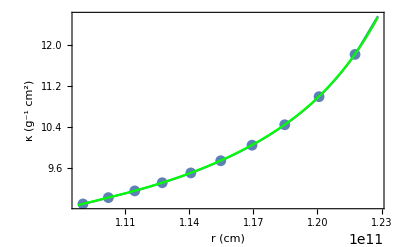

```mathematica
κFit0=Fit[RadiusOpacityReduced,Polinomi,q];
κFit[x_]=κFit0/.{q->x};
Show[Plot[OpacityN[r],{r,RDown,RUp}],ListPlot[RadiusOpacityReduced],Plot[κFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","κ (g^-1 cm^2)","Opacity"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
κ[R_,z_]=κFit[(R^2+z^2)^0.5];
```

```mathematica
σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
Mu=0.62;
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*κ[R,z]*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(κ[R,z]*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
Pr[R_,z_]=ν[R,z]/χ[R,z];
```

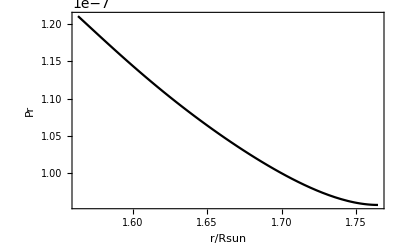

```mathematica
Plotχ=Plot[χ[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},Frame->True,FrameLabel->{"r/Rsun","χ (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
Show[LogPlot[ν[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,1000}}],LogPlot[νdyn[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black,Dashed],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,1000}}],LogPlot[νrad[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black,Dotted],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,1000}}],Frame->True,FrameLabel->{"r/Rsun","ν (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
PlotPr=Plot[Pr[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},Frame->True,FrameLabel->{"r/Rsun","Pr"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black]
```

```mathematica
Ω[R_,z_]:=√(7.4*10^-12);      dLogΩdLogr:=-0.1;
ldR[R_,z_]:=Ω[R,z]*R*(2+R^2/(R^2+z^2)*dLogΩdLogr);   ldz[R_,z_]:=Ω[R,z]*R*(z/(√(R^2+z^2))*dLogΩdLogr);
LastTermGS[R_,z_,kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*(kR^2+kz^2))/Ω[R,z])(PdR[R,z]-kR/kz Pdz[R,z])(kR/kz σdz[R,z]-σdR[R,z])+(2/(γ*Ω[R,z]*R))(kz^2/(kR^2+kz^2))((χ[R,z]*(kR^2+kz^2))/Ω[R,z])(ldR[R,z]-kR/kz ldz[R,z])+1/γ((χ[R,z]*(kR^2+kz^2))/Ω[R,z])((ν[R,z]*(kR^2+kz^2))/Ω[R,z])^2
```

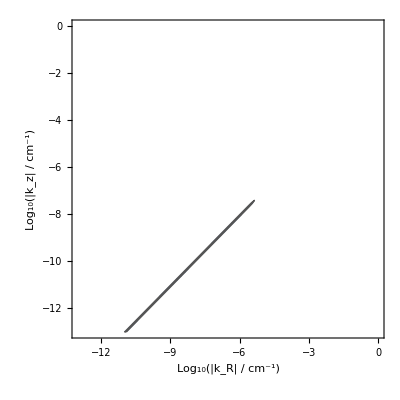
{1.70313,{-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-}}

```mathematica
rper = (RDown+RUp)/2;

Timing[Table[
Rper=rper*Sin[θper];   zper=rper*Cos[θper];

RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0"},BaseStyle->{FontWeight->"Bold",FontSize->8}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->8}]
,{θper,π/36*4,14*π/36,5*π/36}]]
```

```mathematica
(*RadiusMinShear0={{(RUp+RDown)/2,10}}*)
```

```mathematica
RadiusMinShear=Append[RadiusMinShear,{(RUp+RDown)/2,0.1}]
```

{{4.38685×10^8,10},{8.77371×10^8,10},{1.75474×10^9,10},{3.50948×10^9,10},{4.21138×10^9,10},{4.91328×10^9,10},{5.61517×10^9,10},{6.31707×10^9,10},{7.01897×10^9,10},{7.72086×10^9,10},{8.42276×10^9,10},{9.12466×10^9,10},{9.82655×10^9,8.5},{1.01775×10^10,8.},{1.05285×10^10,8.},{1.08794×10^10,7.5},{1.12303×10^10,7.},{1.15813×10^10,6.5},{1.19322×10^10,6.},{1.22832×10^10,5.5},{1.26341×10^10,5.5},{1.29851×10^10,5.5},{1.3336×10^10,5.},{1.3687×10^10,5.},{1.40379×10^10,5.},{1.43889×10^10,4.5},{1.47398×10^10,4.5},{1.50908×10^10,4.5},{1.54417×10^10,4.5},{1.57927×10^10,4.},{1.61436×10^10,4.},{1.68455×10^10,4.},{1.75474×10^10,3.5},{1.82493×10^10,3.5},{1.89512×10^10,3.5},{1.96531×10^10,3.5},{2.10569×10^10,3.},{2.28116×10^10,3.},{2.45664×10^10,2.5},{2.80759×10^10,2.},{2.98306×10^10,2.},{3.15854×10^10,2.},{3.33401×10^10,1.5},{3.68496×10^10,1.3},{4.03591×10^10,1.2},{4.38685×10^10,1.},{4.7378×10^10,0.9},{5.08875×10^10,0.8},{5.4397×10^10,0.7},{5.96612×10^10,0.6},{6.40481×10^10,0.5},{6.66802×10^10,0.5},{7.01897×10^10,0.4},{7.36992×10^10,0.4},{7.72086×10^10,0.4},{8.07181×10^10,0.3},{8.59824×10^10,0.3},{8.94918×10^10,0.3},{9.12466×10^10,0.2},{9.47561×10^10,0.2},{1.01775×10^11,0.2},{1.08794×10^11,0.2},{1.08794×10^11,0.2},{1.12303×10^11,0.2},{1.15813×10^11,0.1}}

```mathematica
RadiusMinShear=Drop[RadiusMinShear,-1]
```

{{4.38685×10^8,10},{8.77371×10^8,10},{1.75474×10^9,10},{3.50948×10^9,10},{4.21138×10^9,10},{4.91328×10^9,10},{5.61517×10^9,10},{6.31707×10^9,10},{7.01897×10^9,10},{7.72086×10^9,10},{8.42276×10^9,10},{9.12466×10^9,10},{9.82655×10^9,8.5},{1.01775×10^10,8.},{1.05285×10^10,8.},{1.08794×10^10,7.5},{1.12303×10^10,7.},{1.15813×10^10,6.5},{1.19322×10^10,6.},{1.22832×10^10,5.5},{1.26341×10^10,5.5},{1.29851×10^10,5.5},{1.3336×10^10,5.},{1.3687×10^10,5.},{1.40379×10^10,5.},{1.43889×10^10,4.5},{1.47398×10^10,4.5},{1.50908×10^10,4.5},{1.54417×10^10,4.5},{1.57927×10^10,4.},{1.61436×10^10,4.},{1.68455×10^10,4.},{1.75474×10^10,3.5},{1.82493×10^10,3.5},{1.89512×10^10,3.5},{1.96531×10^10,3.5},{2.10569×10^10,3.},{2.28116×10^10,3.},{2.45664×10^10,2.5},{2.80759×10^10,2.},{2.98306×10^10,2.},{3.15854×10^10,2.},{3.33401×10^10,1.5},{3.68496×10^10,1.3},{4.03591×10^10,1.2},{4.38685×10^10,1.},{4.7378×10^10,0.9},{5.08875×10^10,0.8},{5.4397×10^10,0.7},{5.96612×10^10,0.6},{6.40481×10^10,0.5},{6.66802×10^10,0.5},{7.01897×10^10,0.4},{7.36992×10^10,0.4},{7.72086×10^10,0.4},{8.07181×10^10,0.3},{8.59824×10^10,0.3},{8.94918×10^10,0.3},{9.12466×10^10,0.2},{9.47561×10^10,0.2},{1.01775×10^11,0.2},{1.08794×10^11,0.2},{1.08794×10^11,0.2},{1.12303×10^11,0.2}}

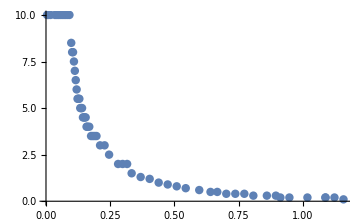

```mathematica
ListPlot[RadiusMinShear]
```

```mathematica
RadiusMinShearFinal={{4.38685*10^8,10},{8.77371*10^8,10},{1.75474*10^9,10},{3.50948*10^9,10},{4.21138*10^9,10},{4.91328*10^9,10},{5.61517*10^9,10},{6.31707*10^9,10},{7.01897*10^9,10},{7.72086*10^9,10},{8.42276*10^9,10},{9.12466*10^9,10},{9.82655*10^9,8.5},{1.01775*10^10,8.},{1.05285*10^10,8.},{1.08794*10^10,7.5},{1.12303*10^10,7.},{1.15813*10^10,6.5},{1.19322*10^10,6.},{1.22832*10^10,5.5},{1.26341*10^10,5.5},{1.29851*10^10,5.5},{1.3336*10^10,5.},{1.3687*10^10,5.},{1.40379*10^10,5.},{1.43889*10^10,4.5},{1.47398*10^10,4.5},{1.50908*10^10,4.5},{1.54417*10^10,4.5},{1.57927*10^10,4.},{1.61436*10^10,4.},{1.68455*10^10,4.},{1.75474*10^10,3.5},{1.82493*10^10,3.5},{1.89512*10^10,3.5},{1.96531*10^10,3.5},{2.10569*10^10,3.},{2.28116*10^10,3.},{2.45664*10^10,2.5},{2.80759*10^10,2.},{2.98306*10^10,2.},{3.15854*10^10,2.},{3.33401*10^10,1.5},{3.68496*10^10,1.3},{4.03591*10^10,1.2},{4.38685*10^10,1.},{4.7378*10^10,0.9},{5.08875*10^10,0.8},{5.4397*10^10,0.7},{5.96612*10^10,0.6},{6.40481*10^10,0.5},{6.66802*10^10,0.5},{7.01897*10^10,0.4},{7.36992*10^10,0.4},{7.72086*10^10,0.4},{8.07181*10^10,0.3},{8.59824*10^10,0.3},{8.94918*10^10,0.3},{9.12466*10^10,0.2},{9.47561*10^10,0.2},{1.01775*10^11,0.2},{1.08794*10^11,0.2},{1.08794*10^11,0.2},{1.12303*10^11,0.2},{1.15813*10^11,0.1}};
```